# Projekt

## Pridobivanje podatkov

Podatke bom vzel iz Wolfram data repository.

```mathematica
podatki = ResourceData["Child Mortality from Malaria"];
```

## Prikaz podatkov nekaterih držav v Afriki, Aziji in Južni Ameriki

Naslednje države sem si izbral, saj so to bile po podatkih dobljenih predvsem na spletnih straneh organizacije WHO države z največjo umrljivostjo po kontinentih.

### Afrika

Te države sem si izbral, saj se tam zgodi skoraj 50% vseh smrtnih primerov zaradi malarije na svetovni ravni.

```mathematica
drzaveAfrika = {LinguisticAssistant,LinguisticAssistant,LinguisticAssistant,LinguisticAssistant};
drzaveAfrikaVrstice=Select[podatki,MemberQ[ drzaveAfrika,#["Country"]]&];
```

Prikaz števila smrtnih primerov za otroke v starostnem razponu 0 - 27 dni ter 0 - 4 let.

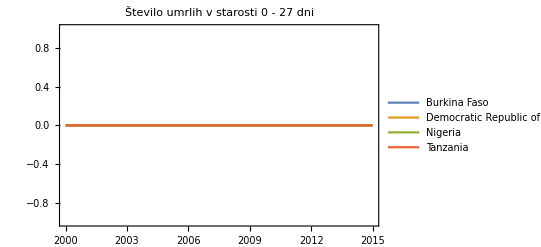

```mathematica
DateListPlot[#["Aged0To27Days"]&/@drzaveAfrikaVrstice,PlotLegends->Table[drzaveAfrikaVrstice[[x]]["Country"],{x,1,4}],PlotLabel->"Število umrlih v starosti 0 - 27 dni"]
```

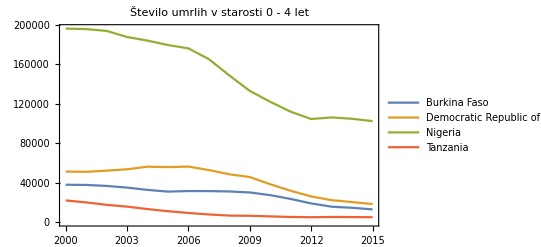

```mathematica
DateListPlot[#["Aged0To4Years"]&/@drzaveAfrikaVrstice,PlotLegends->Table[drzaveAfrikaVrstice[[x]]["Country"],{x,1,4}],PlotLabel->"Število umrlih v starosti 0 - 4 let"]
```

### Azija

```mathematica
drzaveAzija = {LinguisticAssistant,LinguisticAssistant,LinguisticAssistant,LinguisticAssistant};
drzaveAzijaVrstice=Select[podatki,MemberQ[ drzaveAzija,#["Country"]]&];
```

Prikaz števila smrtnih primerov za otroke v starostnem razponu 0 - 4 let .

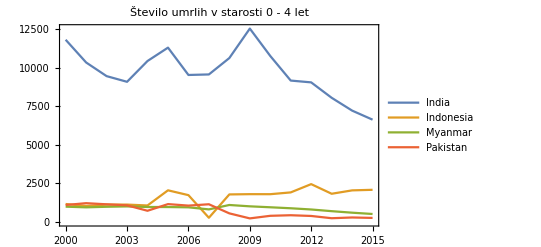

```mathematica
DateListPlot[#["Aged0To4Years"]&/@drzaveAzijaVrstice,PlotLegends->Table[drzaveAzijaVrstice[[x]]["Country"],{x,1,4}],PlotLabel->"Število umrlih v starosti 0 - 4 let"]
```

### Južna Amerika in Karibi

```mathematica
drzaveAmerika = {LinguisticAssistant,LinguisticAssistant,LinguisticAssistant,LinguisticAssistant};
drzaveAmerikaVrstice=Select[podatki,MemberQ[ drzaveAmerika,#["Country"]]&];
```

Prikaz števila smrtnih primerov za otroke v starostnem razponu 0 - 4 let .

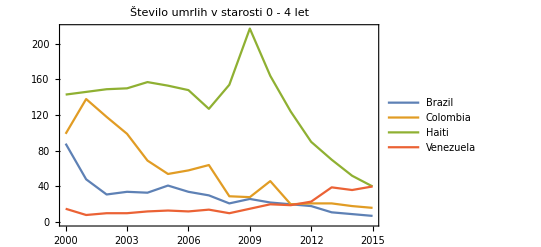

```mathematica
DateListPlot[#["Aged0To4Years"]&/@drzaveAmerikaVrstice,PlotLegends->Table[drzaveAmerikaVrstice[[x]]["Country"],{x,1,4}], PlotLabel->"Število umrlih v starosti 0 - 4 let"]
```